General::munfl: (3.66374×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

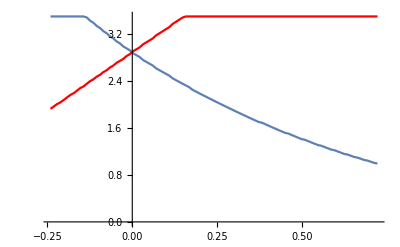

avecphasediagram.csv

critsigmaphasediagram_2cycleonset_henon.csv

critsigmaphasediagram_opper_henon.csv

```mathematica
Clear["Global`*"];

b=0.3;
alpha=0.5;
K = 2.0;

numsig = 200;
sigmin = 0.9; 
sigmax = Sqrt[3.5];
sigmavec = Table[s,{s, sigmin, sigmax, (sigmax - sigmin)/(numsig -1)}];


numa = 100;
amax = -((-1+alpha b)^2/(4 alpha (alpha-K+alpha K))); 
amin = (-1+alpha b)^2/(4 alpha (-alpha-K+alpha K));
avec = Table[r,{r, amin, amax, (amax - amin)/(numa -1)}];
critsigmavec = Table[r,{r, amin, amax, (amax - amin)/(numa -1)}];

critsigmavecopper = Table[r,{r, amin, amax, (amax - amin)/(numa -1)}];

Monitor[Monitor[For[j=1, j<numa+1,j++,
a= avec[[j]];
fvec = Table[0,{s, sigmin, sigmax, (sigmax - sigmin)/(numsig -1)}];
fvec2 = Table[0,{s, sigmin, sigmax, (sigmax - sigmin)/(numsig -1)}];
For[i = 1, i<numsig+1, i++,
sigma = sigmavec[[i]];
qmin = 0.001;
qmax = 4.0;
numq = 101;
qvec = Table[myq, {myq, qmin, qmax, (qmax-qmin)/(numq-1)}];

gvec = Table[100, {myq, qmin, qmax, (qmax-qmin)/(numq-1)}];


Monitor[Do[


q = qvec[[k]];

myq= NIntegrate[(((b-1/alpha)+ Sqrt[(b-1/alpha)^2+ 4 a (1+ (1-alpha)/alpha eta)])/(2a))^2Exp[-eta^2/(2 sigma^2 q)]/Sqrt[2Pi sigma^2 q],{eta,-2, 2}]+ (1/2)  Erfc[√2 √(1/(q sigma^2))](((b-1/alpha)+ Sqrt[(b-1/alpha)^2+ 4 a (1+ 2(1-alpha)/alpha )])/(2a))^2 + (1/2)  Erfc[√2 √(1/(q sigma^2))](((b-1/alpha)+ Sqrt[(b-1/alpha)^2+ 4 a (1- 2(1-alpha)/alpha )])/(2a))^2;
fvec[[i]]=(myq-q)^2;



,{k, 1, numq}];,k];

nearest = Min[Abs[gvec]];
pos = Position[Abs[gvec], nearest][[1,1]];
q = qvec[[pos]];

fvec[[i]]= NIntegrate[Exp[-eta^2/(2 sigma^2 q)]/Sqrt[2Pi sigma^2 q]sigma^2(1-alpha)^2/Abs[(-1)^2 + 2 alpha a (((b-1/alpha)+ Sqrt[(b-1/alpha)^2+ 4 a (1+ (1-alpha)/alpha eta)])/(2a))(-1)- alpha b]^2,{eta, -2, 2}] ;
fvec2[[i]]= NIntegrate[Exp[-eta^2/(2 sigma^2 q)]/Sqrt[2Pi sigma^2 q]sigma^2(1-alpha)^2/Abs[(1)^2 + 2 alpha a (((b-1/alpha)+ Sqrt[(b-1/alpha)^2+ 4 a (1+ (1-alpha)/alpha eta)])/(2a))(1)- alpha b]^2,{eta, -2, 2}] ;


];
nearest = Nearest[fvec,1][[1]];
pos = Position[fvec, nearest][[1,1]];
critsigmavec[[j]]= sigmavec[[pos]];

nearest = Nearest[fvec2,1][[1]];
pos = Position[fvec2, nearest][[1,1]];
critsigmavecopper[[j]]= sigmavec[[pos]];
];,j];,i];



plt1 = ListLinePlot[Transpose[{ avec,critsigmavec^2}], PlotRange->All];
plt2 = ListLinePlot[Transpose[{ avec,critsigmavecopper^2}], PlotRange->All, PlotStyle->{Red}];
Show[plt1, plt2]
SetDirectory[NotebookDirectory[]];
Export["avecphasediagram.csv",avec]
Export["critsigmaphasediagram_2cycleonset_henon.csv", critsigmavec]
Export["critsigmaphasediagram_opper_henon.csv", critsigmavecopper]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["avecphasediagram.csv",avec]
Export["critsigmaphasediagram_2cycleonset_henon.csv", critsigmavec]
Export["critsigmaphasediagram_opper_henon.csv", critsigmavecopper]
```

avecphasediagram.csv

critsigmaphasediagram_2cycleonset_henon.csv

critsigmaphasediagram_opper_henon.csv

```mathematica
N[Sqrt[2]]
```

1.41421

```mathematica
0.2^2
```

0.04

```mathematica
fvec2
```

{0.0305189,0.0319194,0.0334469,0.0352838,0.0370495,0.0471176,0.0416151,0.0456682,0.0463375,0.0495343,0.0547055,0.0590096,0.0676899,0.298853,0.0893306,0.183117,0.160572,2.64455,0.296703,0.580137,0.471713,0.691513,32.6281,1.71416,21.8659,4.75238,8.27293,299.576,12.2104,127.503,34.0672,117.534,58.5732,28322.6,76.7327,451.439,78.7081,740.633,229.971,244.291,3993.52,1459.06,338.963,3656.78,803.899,523.333,1117.74,1132.07,1110.79,8116.08,8116.08,1110.79,1132.07,1117.74,523.333,803.899,3656.78,338.963,1459.06,3993.52,244.291,229.971,740.633,78.7081,451.439,76.7327,28322.6,58.5732,117.534,34.0672,127.503,12.2104,299.576,8.27293,4.75238,21.8659,1.71416,32.6281,0.691513,0.471713,0.580137,0.296703,2.64455,0.160572,0.183117,0.0893306,0.298853,0.0676899,0.0590096,0.0547055,0.0495343,0.0463375,0.0456682,0.0416151,0.0471176,0.0370495,0.0352838,0.0334469,0.0319194,0.0305189}

```mathematica
N[critl1vec]
```

{-10.,-0.909091,-1.71717,-2.32323,-3.13131,-3.93939,-4.74747,-5.55556,-6.36364,-7.17172}

```mathematica
Clear["Global`*"];

r = 1.5;


numsig = 100;
sigmin = 0.01; 
sigmax = Sqrt[2];
sigmavec = Table[s,{s, sigmin, sigmax, (sigmax - sigmin)/(numsig -1)}];
fvec = Table[0,{s, sigmin, sigmax, (sigmax - sigmin)/(numsig -1)}];
For[i = 1, i<numsig+1, i++,
sigma= sigmavec[[i]];
start = (1-1/r)^2;
sol = FindRoot[(ⅇ^(-(-1+1/r)^2/(2 q sigma^2)) √q (-1+r) r sigma-ⅇ^(-1/(2 q r^2 sigma^2)) √q r (-1+2 r) sigma-√(π/2) (1+r (-2+r+q r sigma^2)) Erf[(-1+1/r)/(√2 √q sigma)]+√(π/2) (1+r (-2+r+q r sigma^2)) Erf[1/(√2 √q r sigma)])/(√(2 π) r^2)+1/2 Erfc[1/(√2 √q r sigma)]==q,{q, start}];
q0 = q/.sol;

phi1 =(√q0 sigma (-1+√q0 √(1/(q0 sigma^2)) sigma+Erfc[1/(√2 √q0 r sigma)]))/(2 √(q0 sigma^2));
fvec[[i]] = NIntegrate[sigma^2 Exp[-(myx-(1-1/r ))^2/(2 sigma^2 q0)]/Sqrt[2 Pi sigma^2 q0] r^2myx^2/((2 - r myx )^2),{myx, 0, 1}] +  phi1 r^2sigma^2/((1 - r )^2);

];
nearest = Nearest[fvec,1][[1]];
pos = Position[fvec, nearest][[1,1]];
critsigma= sigmavec[[pos]]
```

General::munfl: Exp[-20000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3419.59] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.90359

```mathematica
Clear["Global`*"];
Integrate[Exp[-(x-1+1/r)^2/(2 sigma^2 q0)]/Sqrt[2Pi sigma^2 q0],{x, 0,1}]
```

```mathematica
(-Erf[(-1+1/r)/(√2 √q0 sigma)]+Erf[1/(√2 √q0 r sigma)])/2
```

```mathematica
Clear["Global`*"];
Solve[g == r x /(u + r x -  gamma r x s^2 g ), g]
```

{{g→(u+r x-√(-4 gamma r^2 s^2 x^2+(-u-r x)^2))/(2 gamma r s^2 x)},{g→(u+r x+√(-4 gamma r^2 s^2 x^2+(-u-r x)^2))/(2 gamma r s^2 x)}}

```mathematica
Series[(u+r x+√(-4 r^2 s^2 x^2+(-u-r x)^2))/(2 r s^2 x)/.u->1/w, {w, 0, 1}]
```

(1+√(1/w^2) w)/(2 r s^2 x w)+(1+√(1/w^2) w)/(2 s^2)-r √(1/w^2) w x w+O[w]^2

```mathematica
Series[(u+r x+√(-4 gamma r^2 s^2 x^2+(-u-r x)^2))/(2 gamma r s^2 x), {u, 0, 1}]
```

(r x+√(-r^2 (-1+4 gamma s^2) x^2))/(2 gamma r s^2 x)+((1+(r x)/(√(-r^2 (-1+4 gamma s^2) x^2))) u)/(2 gamma r s^2 x)+O[u]^2